```mathematica
Get[FileNameJoin[{NotebookDirectory[], "GeneticAlgorithmPackage.wl"}]]
Get[FileNameJoin[{NotebookDirectory[], "ProgramEvolutionPackage.wl"}]]
```

## Landscape Animation

```mathematica
ClearAll[fDistr, init3];
fDistr[x_] := N[PDF[MultinormalDistribution[{3,3},{{1,-1/3},{-1/3,2/3}}], x]];
init3 = {1, 1};
 
result = GeneticAlgorithm[init3, fDistr];
result = Transpose[result];
```

population = {{1,1},{1.26296,1.08419},{1.03326,0.910334}}

population = {{1.14811,0.997263},{1.26296,1.08419},{1.26296,1.08419}}

population = {{1.26296,1.08419},{1.26296,1.08419},{1.26296,1.08419}}

population = {{1.26296,1.08419},{1.26296,1.08419},{1.32082,0.913727}}

population = {{1.32082,0.913727},{1.30519,1.13273},{1.26296,1.08419}}

population = {{1.29189,0.998959},{1.26296,1.08419},{1.14828,1.37716}}

population = {{1.14828,1.37716},{0.924239,1.35441},{1.14828,1.37716}}

population = {{0.876369,1.3754},{1.14828,1.37716},{1.14828,1.37716}}

population = {{0.867411,1.56586},{1.14828,1.37716},{1.14828,1.37716}}

population = {{1.05387,1.47788},{1.14828,1.37716},{1.01347,1.73618}}

```mathematica
plot3D=Plot3D[fDistr[{x, y}], {x, 0, 5}, {y, 0, 5}, AspectRatio->Automatic, ColorFunction->"Rainbow", Mesh->None, PlotPoints->25,BoxRatios->{1, 1, 1}];
```

```mathematica
graphics=Table[Graphics3D[{Black, PointSize->Medium,
			Point[{#[[i]][[1]], #[[i]][[2]], fDistr[{#[[i]][[1]], #[[i]][[2]]}]}& /@ result]}, 
			PlotRange->{{0,5},{0,5}, Automatic}
		],
		{i, 1, Length[First[result]]}];
```

```mathematica
Manipulate[		
	Show[
		plot3D,
		graphics[[i]],
		Boxed->False, Axes->False		
	],
	{i, 1, Length[First[result]],1}
]
```

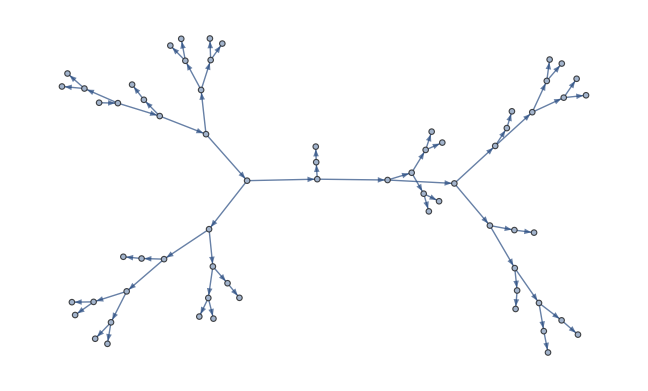

```mathematica
graph = Graph[{{expr,1,9384}->{expr,2,4972},{expr,2,4972}->{exprX,1,8102},{expr,2,4972}->{exprX,1,8414},{expr,1,9384}->{expr,1,7032},{expr,1,7032}->{expr,1,473},{expr,1,473}->{expr,1,9918},{expr,1,9918}->{expr,2,1253},{expr,2,1253}->{exprX,1,5152},{expr,2,1253}->{exprX,1,6303},{expr,1,9918}->{expr,2,977},{expr,2,977}->{exprX,1,4763},{expr,2,977}->{exprX,1,3970},{expr,1,473}->{expr,1,6213},{expr,1,6213}->{expr,1,3353},{expr,1,3353}->{expr,1,2162},{expr,1,2162}->{expr,2,4778},{expr,2,4778}->{exprX,1,9726},{expr,2,4778}->{exprX,1,1505},{expr,1,2162}->{expr,3,8510},{expr,3,8510}->{exprX,1,2907},{expr,1,3353}->{expr,1,8502},{expr,1,8502}->{expr,1,5101},{expr,1,5101}->{expr,2,7388},{expr,2,7388}->{exprX,1,36},{expr,2,7388}->{exprX,1,7113},{expr,1,5101}->{expr,2,4111},{expr,2,4111}->{exprX,1,2},{expr,2,4111}->{exprX,1,4864},{expr,1,8502}->{expr,3,1957},{expr,3,1957}->{exprX,1,69},{expr,1,6213}->{expr,1,587},{expr,1,587}->{expr,3,7684},{expr,3,7684}->{exprX,1,6469},{expr,1,587}->{expr,1,7542},{expr,1,7542}->{expr,1,4058},{expr,1,4058}->{expr,1,6210},{expr,1,6210}->{expr,3,4231},{expr,3,4231}->{exprX,1,4380},{expr,1,6210}->{expr,1,7546},{expr,1,7546}->{expr,2,9812},{expr,2,9812}->{exprX,1,1058},{expr,2,9812}->{exprX,1,2659},{expr,1,7546}->{expr,2,6458},{expr,2,6458}->{exprX,1,997},{expr,2,6458}->{exprX,1,7620},{expr,1,4058}->{expr,1,8665},{expr,1,8665}->{expr,1,9848},{expr,1,9848}->{expr,3,5946},{expr,3,5946}->{exprX,1,7477},{expr,1,9848}->{expr,1,9905},{expr,1,9905}->{expr,3,1141},{expr,3,1141}->{exprX,1,6734},{expr,1,9905}->{expr,3,3829},{expr,3,3829}->{exprX,1,6724},{expr,1,8665}->{expr,3,9404},{expr,3,9404}->{exprX,1,6967},{expr,1,7542}->{expr,1,7633},{expr,1,7633}->{expr,2,7443},{expr,2,7443}->{exprX,1,2808},{expr,2,7443}->{exprX,1,9886},{expr,1,7633}->{expr,2,3493},{expr,2,3493}->{exprX,1,2431},{expr,2,3493}->{exprX,1,664},{expr,1,7032}->{expr,3,8369},{expr,3,8369}->{exprX,1,1913},{root,1,6832}->{expr,1,9384}}]
```

Function[x, 2-4/x^6-2/x^5+20/x^3-4/x^2-12/x-5 x+12 x^2+9 x^3+20 x^4-5 x^5]